# Fourier analysis

```mathematica
SetOptions[ListPlot,PlotRange->All,Joined->True,AspectRatio->0.4];
SetOptions[ArrayPlot,ColorFunction->GrayLevel, Frame->False];
```

## Section. Fourier Series

Fourier analysis is the mathematical description of periodic signals as sums of Cos and Sin functions. It is one of the most popular and useful theories for the analysis of signals, such as acoustical sounds in 1D and images in 2D.

The basic reason for its usefulness is that a temporal (or spatial) periodic signal can be transformed in a "Fourier series", and that it is often easier to do signal operations like filtering or even differentiation on this transformed signal. Let us look at an arbitrary sum of Sin and Cos functions:

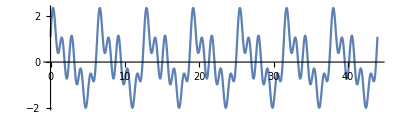

```mathematica
Plot[Sin[t]+0.37 Sin[2 t]+0.23 Sin[3 t]+0.74 Sin[5 t]+0.4 Cos[t]+0.59 Cos[2 t]+0.11 Cos[4 t],{t,0,14 π},AspectRatio->0.3]
```

This is a periodic function, and because we took the timescale from 0 to 14π, we get 7 periods of the lowest frequency (Sin[t]). This is the base frequency. The higher frequencies, which are multiples of the base frequency, are called the harmonics. We can make an infinite number of periodic functions this way. The amplitude factors in front of the Sin (1, 0.37, 0.23, 0, 0.74) and Cos (0.4, 0.59, 0, 1.11, 0) functions are called the Fourier coefficients.

```mathematica
Manipulate[Plot[Sin[t]+a Sin[2 t]+b Sin[3 t]+c Sin[5 t]+d Cos[t]+e Cos[2 t]+f Cos[4 t],{t,0,14 π},AspectRatio->0.3,PlotRange->{-2,2}],{{a,0.37},-1,1},{{b,0.23},-1,1},{{c,0.74},-1,1},{{d,0.4},-1,1},{{e,0.59},-1,1},{{f,0.11},-1,1}]
```

```mathematica
Manipulate[Play[Sin[1000t]+a Sin[2000 t]+b Sin[3000 t]+c Sin[5000 t]+d Cos[1000t]+e Cos[2000 t]+f Cos[4000 t],{t,0,2}],{{a,0.37},-1,1},{{b,0.23},-1,1},{{c,0.74},-1,1},{{d,0.4},-1,1},{{e,0.59},-1,1},{{f,0.11},-1,1}]
```

It also works the other way: we can make from a given periodic signal the Sin and Cos series: This was first found by the Frenchman Jean-Baptiste Fourier (1822): "Every periodic function can be written as a series of Cos and Sin fuctions with increasing frequency":

```mathematica
f[t]=Subscript[a, 0]+∑_(k=1)^∞ Subscript[a, k] Cos[k t ]+∑_(l=1)^∞ Subscript[b, l] Sin[l t ]
```

with a_0 the average value, a_k the Fourier coefficient of the Cos series, and b_lthe Fourier coefficient of the Sin series.

Jean-Baptiste Joseph Fourier (1768 - 1830).

Fourier proved that the Fourier coefficients can be calculated from the signal with the following formula's (which are discussed and proved in section 10.4.3 in the math section of the reader):

```mathematica
Subscript[a, 0]=1/(2π)∫_-π^π f[t]ⅆt;
Subscript[a, k]=1/π∫_-π^π f[t]Cos[k t]ⅆt;
Subscript[b, l]=1/π∫_-π^π f[t]Sin[l t]ⅆt;
```

In 10.4.5 examples are given how to calculate a_kand b_l for some easy periodic functions, i.e. functions that can be easily described such as by straight lines (f[x]=(|x|)/π → a triangle, f[x]= -1 and 1 → a block function). Only for such easy functions we are able to calculate the integrals for a_kand b_l analytically, i.e. by hand.

Every sinusoidal function is fully described by its amplitude, frequency and its phase. The graph of the amplitudes as a function of frequency is the amplitude spectrum, the graph of the phases as a function of frequency is the phase spectrum.

E.g. the sawtooth function with period p seconds (so the frequency is 1/p Hz) and amplitude a (given here with a base frequency and 3 harmonics, but in fact there are an infinite number of harmonics necessary to make the true sawtooth function):

```mathematica
sawtooth[t_]:=a/2+(2a)/π(Sin[(2π t)/p]-1/2 Sin[(4π t)/p]+1/3 Sin[(6π t)/p]-1/4 Sin[(8π t)/p]);
```

```mathematica
sawtooth[t_,n_]:=a/2+(2a)/π∑_(m=1)^n (-1)^(m+1)1/m Sin[(2m π t)/p]
```

We see that the truncated series with only 4 frequencies does only approximate the sawtooth function:

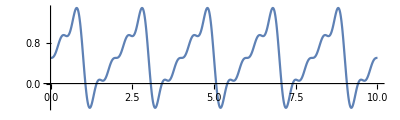

```mathematica
a=1;p=2;Plot[sawtooth[t],{t,0,10},AspectRatio->0.3,PlotPoints->200]
```

```mathematica
a=1;p=2;Plot[sawtooth[t,10],{t,0,10},AspectRatio->0.3,PlotPoints->200]
```

-Graphics-

When we plot the base frequency (and the average) also in the graph, we see the basic periodicity:

```mathematica
a=1;p=2;Plot[{sawtooth[t],a/2+((2 a) Sin[(2 π t)/p])/π},{t,0,10},AspectRatio->0.3]
```

The average is a/2 = 1/2 and we can see this in the graph. We can also say that this is the Fourier coefficient of the lowest possible frequency, which is zero. Zero frequency is a signal that does not fluctuate at all, in other words: a constant signal.

So we have the frequencies {0, 1/p, 2/p, 3/p, 4/p} and at these frequencies we have the amplitudes {a/2, (2a)/π, -a/π,(2a)/(3π),-a/(2π)} and the phases {0, 0, π, 0, π}. We define the phase of the average to be 0. We plot the amplitude and phase spectra of this function:

```mathematica
ampl=ListPlot[{{0,a/2},{1/p,(2 a)/π},{2/p,-a/π},{3/p,(2 a)/(3 π)},{4/p,-a/(2 π)}},PlotStyle->PointSize[0.03],Filling->Axis,Joined->False,AspectRatio->0.5]
```

```mathematica
phase=ListPlot[{{0,0},{1/p,0},{2/p,π},{3/p,0},{4/p,π}},PlotStyle->PointSize[0.03],Filling->Axis,Joined->False,AspectRatio->0.5];GraphicsGrid[{{ampl,phase}}]
```

Signals with fast (steep) variations are build from high frequency wave functions, and vice versa.

Filtering is cutting out frequencies from the spectrum. 
E.g. when we want to cancel low frequency noise (e.g. slow variations in an EEG signal) we apply a high-pass filter. Other slow variation noise sources are 50 Hz noise and, in images, light variations due to overcast shadows. 
When we want to reduce high frequency noise (e.g. speckle noise in images) we apply a low-pass filter.

In the Fourier domain a filter can be very simple. For example: a stepfunction which is zero for 0 < x < 1.75, and one for x > 1.75. When we multiply the spectrum with this filter, we make the Fourier coefficients for the frequencies {0, 1/2, 1, 3/2} zero and the frequency 2 is the only one left after this high-pass filtering.

Spatial frequencies are variations over space. The wavelength is expressed in meters, the frequency in cycles per meter. Here is an example of a sinusoidal spatial function with increasing frequency in the x-direction:

```mathematica
ArrayPlot[Table[Sin[t^2.2],{y,0,10},{t,0,4 π,0.01}],AspectRatio->0.2]
```

## Section. Examples of Fourier series

```mathematica
Off[General::"spell1"];
Off[NIntegrate::"ploss"];
Off[NIntegrate::"ncvb"];
Off[NIntegrate::"inum"];
Off[NIntegrate::"slwcon"];
Off[NIntegrate::"oidiv"];
```

To make even functions with period 2L, we can start with  the zigzag function.

```mathematica
zigzag[x_]:=1-2Abs[x/(2L)-1/2-Floor[x/(2L)]]
```

Its graph looks like a zigzag.

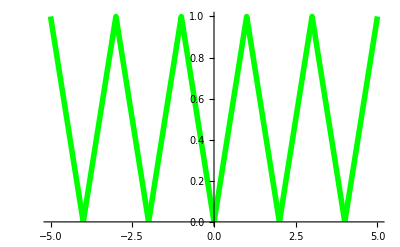

```mathematica
L=1;
Plot[zigzag[x],{x,-5,5},PlotStyle->{{Green,Thickness[.01]}}]
```

Functions defined in terms of the zigzag function are even and periodic.

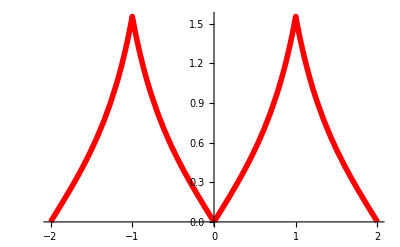

```mathematica
Plot[ Tan[zigzag[x]],{x,-2,2},PlotStyle->{{Red,Thickness[.01]}}]
```

This defines a block function with amplitude amp and period 2L:

```mathematica
f[x_]:= If[zigzag[x]<1/2,amp,0]
```

Have a look, with rather arbitrary choices for amp and L:

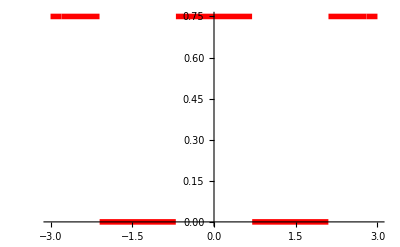

```mathematica
amp=3/4;L=1.4;
Plot[f[x],{x,-3,3},PlotPoints->100,
	PlotStyle ->{Red,Thickness[0.01]}]
```

The Fourier coefficients of this even function f are defined by:

```mathematica
Clear[a];
a[0]=1/(2L)NIntegrate[f[t], {t, -L, L}];
a[n_] :=a[n]=
1/L NIntegrate[f[t] Cos[(π n t)/L], {t, -L, L}];
b[l_] :=b[l]=
1/L NIntegrate[f[t] Sin[(π l t)/L], {t, -L, L}];
```

```mathematica
b[2]
```

0.

```mathematica
b[4]
```

0.

```mathematica
|
```

The first few Fourier coefficients:

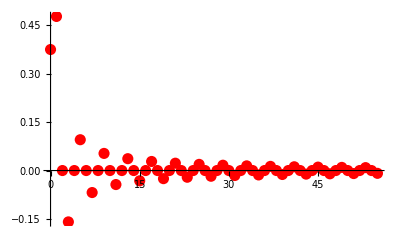

```mathematica
ListPlot[Table[{n,a[n]},{n,0,55}],PlotRange->All,Joined->False,PlotStyle->{Red,PointSize[.02]}]
```

Because the function is symmetric around zero, the Sin components are all zero:

```mathematica
ListPlot[Table[{l,b[l]},{l,0,55}],PlotRange->All,PlotStyle->{Blue,PointSize[.01]}]
```

We show a few approximations of f by partial sums of its Fourier series.

```mathematica
plottot[grens_,opt___]:=(approx[x_]=∑_(n=0)^grens a[n] Cos[(π n x)/L];Plot[{f[x],approx[x]},{x,-2,2},opt]);
```

```mathematica
Manipulate[plottot[n,PlotPoints->200,PlotRange->{-0.25 amp,1.2 amp},PlotStyle->{{Red,Thickness[0.01]},{Green,Thickness[0.01]}}],{n,1,20,1}]
```

```mathematica
sum55=plottot[55,PlotPoints->200]
```

The Gibbs phenomenon in closeup:

```mathematica
Show[sum55,PlotRange->{{0,2},{.6,.86}}]
```

### Fourier applet

## Section. The Fourier transform

### Fourier series

```mathematica
f[t]=Subscript[a, 0]+∑_(k=1)^∞ Subscript[a, k] Cos[k t ]+∑_(l=1)^∞ Subscript[b, l] Sin[l t ]
```

```mathematica
Subscript[a, 0]=1/(2π)∫_-π^π f[t]ⅆt;
Subscript[a, k]=1/π∫_-π^π f[t]Cos[k t]ⅆt;
Subscript[b, l]=1/π∫_-π^π f[t]Sin[l t]ⅆt;
```

### Fourier transform

```mathematica
ExpToTrig[ⅇ^(ⅈ ϕ)]
```

The Fourier transform F(ω) of f(x) is by definition

F(ω)=∫_(-∞)^∞ f(x) e^-iωx ⅆx

The Inverse Fourier transform f(x) of F(ω) is by definition

f(x)=∫_(-∞)^∞ F(ω) e^iωx ⅆx

## Section. Convolution is a product in the Fourier domain: the convolution theorem.

It is often not so easy to calculate the convolution integral. It is often much easier to calculate the integral of the convolution in the Fourier domain. This section explains how this works. We start from the convolution of the function h(x) with the kernel g(x):

f(x)=∫_(-∞)^∞ h(y) g(x-y)ⅆy

The Fourier transform F(ω) of f(x) is then by definition

F(ω)=∫_(-∞)^∞ f(x) e^-iωx ⅆx=∫_(-∞)^∞ ∫_(-∞)^∞ h(y) g(x-y)ⅆy e^-iωx ⅆx

We reorder the terms in the integral and make the substitution x-y=τ, so we have x=τ+y and e^-iωx=e^-iωτ. e^-iωy :

∫_(-∞)^∞ h(y)∫_(-∞)^∞ e^-iωx g(x-y)ⅆx ⅆy = ∫_(-∞)^∞ h(y)∫_(-∞)^∞ e^(-iω(τ+y)) g(τ)ⅆ(τ+y) ⅆy

When we integrate to τ, we keep y constant, so ⅆ(τ+y) is equal to ⅆτ. So we get:

∫_(-∞)^∞ h(y)∫_(-∞)^∞ e^-iωτ e^-iωy g(τ)ⅆτ ⅆy

Because e^-iωy is constant in the integration to τ, we may bring it as a constant outside the integral:

∫_(-∞)^∞ h(y)e^-iωy ⅆy   ∫_(-∞)^∞ e^-iωτ g(τ) ⅆτ = H(ω) . G(ω)

where H(ω) is the Fourier transform of the function h(x) and G(ω) is the Fourier transform of the kernel g(x). So the Fourier transform of a convolution is the product of the Fourier transform of the filter with the Fourier transform of the signal. To put it otherwise:

f(x)  =  h(x) ⊗ g(x)
                    ↕               ↕           ↕
	F(ω) = H(ω) . G(ω)

We can calculate a convolution h⊗g by calculating the Fourier transforms H(ω) and G(ω), multiply them to get F(ω), and we get f(x) by taking the inverse Fourier transform of F(ω). Often this is a much faster method then calculating the convolution integral, because the routines that calculate the Fourier transform are so fast. We look at an example where we filter noise from the data. We simulate a signal of a noisy ECG recording:

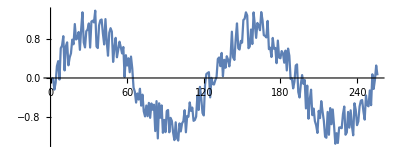

```mathematica
data=Table[N[Sin[(2 π n)/128]+0.8 (Random[]-1/2)],{n,1,256}];
ListPlot[data,Joined->True,AspectRatio->0.4]
```

This generates a typical convolution kernel suitable for smoothing data.

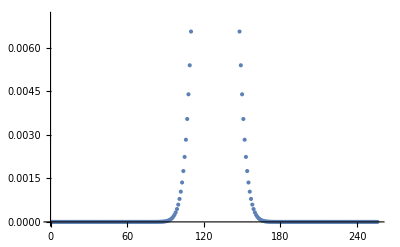

```mathematica
σ=10;
kernel=Table[(ⅇ^(-n^2/(2 σ^2)))/(√(2π σ^2)),{n,-128,127}];ListPlot[kernel]
```

This puts the convolution kernel in a form suitable for use in a discrete Fourier transform (we have to bring it to the origin):

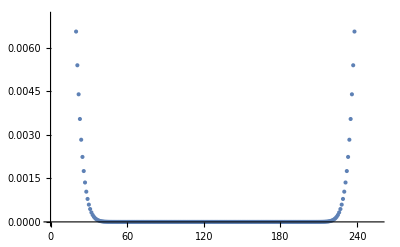

```mathematica
kernel = RotateLeft[kernel, 128];
ListPlot[kernel]
```

The Fourier transform of the data looks like this (a very low frequency and at the higher frequencies the noise):

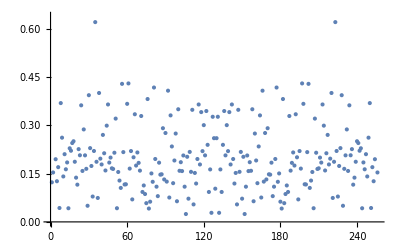

```mathematica
p1=ListPlot[Abs[Fourier[data]]]
```

The Fourier transform of the kernel looks like a low-pass filter:

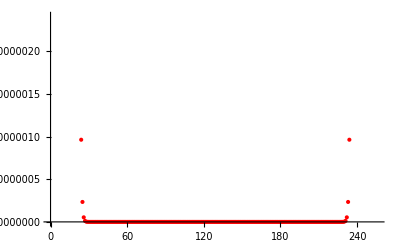

```mathematica
p2=ListPlot[128Abs[Fourier[kernel]],PlotStyle->Red]
```

```mathematica
Show[{p1,p2}]
```

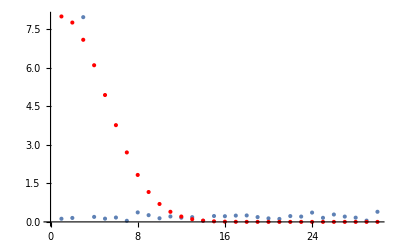

```mathematica
Show[{p1,p2},PlotRange->{{0,30},All}]
```

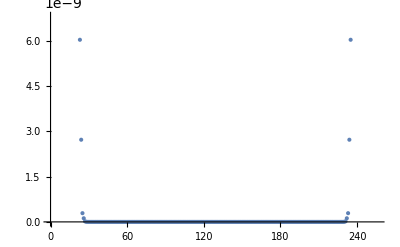

```mathematica
ListPlot[Abs[Fourier[kernel] × Fourier[data]]]
```

See how we cleaned up the spectrum. We are now "in the Fourier domain", and we can go back to our temporal domain by means of the inverse Fourier transform.

The convolution is done by multiplying the Fourier transform of the data by the Fourier transform of the kernel, then taking the inverse Fourier transform of the result.

```mathematica
conv = InverseFourier[Sqrt[256] Fourier[data] Fourier[kernel] ] ;
```

This plots the result. The Chop removes small imaginary parts that are generated in the Fourier transforms. The final plot is a smoothed version of the original data.

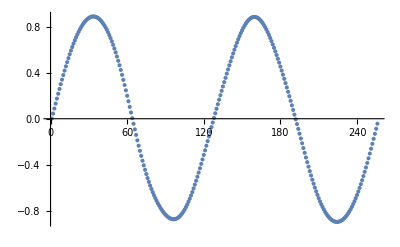

```mathematica
ListPlot[Chop[conv]]
```

Temporal versus frequency domain: There is always the inverse relation: when a wavelength is small in the temporal or spatial domain, it represents a high frequency. A low frequency represents a long wavelength, with a large representation in the temporal/spatial domain. The shortest function, the spike- or delta-function, has all frequencies at aplitude one, with phase zero. The longest (infinite) wavelength has frequency zero.

Removing the high frequencies from a signal (low-pass filtering, blurring) makes the signal less spiky, more smooth. Removing the low frequencies from a signal also removes the average component (the average becomes zero), and slow trends and variations are cancelled.

White noise has a spectrum with all frequencies at amplitude one, and a random phase for each frequency. Pink noise has only amplitudes at a limited band of frequencies. Band-limited noise misses the high or the low frequencies.

If a function is not periodical, is can be made periodical by simple repetition left and right of the original function, from minus infinity to plus infinity. In the spatial domain this means tiling of the whole space with the 2D function.

## Section. A linear system

The system described by a convolution integral is called a linear system. A linear system is characterised by two properties:

f[t] ⊗ h[t] =  g[t] ⇒ 
1. Superposition:	(f_1[t] + f_2[t]) ⊗ h[t] = f_1[t] ⊗ h[t]+ f_2[t] ⊗ h[t] =g_1[t] + g_2[t]  
2. Homogeneity:	a f[t] ⊗ h[t] = a g[t]

E.g. the process of projecting an external line function on the retina is described by such a convolution. The input function f[x,y] is a very narrow line, the output function g[u,v] is the blurred image on the retina, and the kernel h[x,y] is the blurring function, also called the line-spread function (LSF). When a point is projected, we call h[x,y] the point-spread function (PSF).

When all elements of a shifting template are equal and their sum is 1, the filter is called a running average filter. When e.g. the length is 5 (the filter looks like {1/5,1/5,1/5,1/5,1/5} or 1/5{1,1,1,1,1}), it takes the average over 5 samples at each shift position. This is a lowpass filter.

## Section. The response on a spike function: the Point Spread Function (PSF)

We saw earlier that the convolution of a kernel with the delta (spike) function gives the kernel itself:

### The δ-function (1D point impulse)

The smallest possible function, with area 1, is the delta function, also known as the Dirac function, or the impulse function. This function is defined by:

```mathematica
δ[x]=0, x≠0
∫_(-∞)^∞ f[x]δ[x]ⅆx=f[0]
```

In Mathematica, this function can by called by DirecDelta.

```mathematica
Clear[f]
```

```mathematica
∫_(-∞)^∞ f[x]DiracDelta[x]ⅆx
```

f[0]

An important property is the selection of a specific value of f[x] on the x-axis, when we shift the delta function to that position. This is the the sifting property of the delta function:

```mathematica
Assuming[a∈Reals,∫_(-∞)^∞ f[x]DiracDelta[x-a]ⅆx]
```

f[a]

Suppose we like to see the shape of our convolution kernel. The solution is to take the spike image as input:

```mathematica
lettera=ImageData[Import["http://bmia.bmt.tue.nl/people/BRomeny/Courses/8C080/a.gif"]]⟦All,All,1⟧;
```

```mathematica
spike=Table[0,{200},{200}];spike⟦100,100⟧=1;
ArrayPlot[spike]
```

-Graphics-

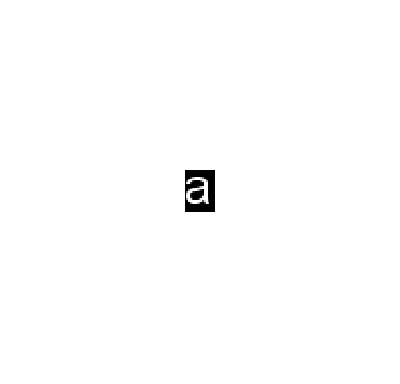

```mathematica
ArrayPlot[ListConvolve[lettera,spike]]
```

If one wants to determine how good an imaging system is, one needs to know how a very tiny point is imaged. E.g. in a CT scanner one can make an image of a very thin (100 μm) copper wire. This functions as a delta funtion, and the image measured gives the Point Spread Funtion, which is a measure for the quality (spatial resolution). Recall the measurements on the human retina in the bginning.

The Fourier transform of the PSF is called the Modulation Transfer Function.

A frequently applied filter is the Gaussian function:

```mathematica
Unprotect[gauss];
```

PS: The function gauss[] is already defined in the package MathVisionTools, and protected. After 'Unprotect' we can define it anew.

```mathematica
gauss[x_]:=1/(√(2π σ^2))E^(-x^2/(2 σ^2))
```

Remarkably, the Fourier transform of a spatial Gaussian function, as a function of x, is also a Gaussian function, of course as a function of spatial frequency ω:

```mathematica
σ=.;
Simplify[FourierTransform[1/(√(2π σ^2))E^(-x^2/(2 σ^2)),x,ω],σ>0]
```

(ⅇ^(-1/2 σ^2 ω^2))/(√(2 π))

So, we can do Gaussian blurring (for noise removal) in the spatial domain with the convolution with a Gaussian kernel, or in the frequency domain, with a Gaussian kernel!

Note that the σ is now as a multiplier, so a narrow Gaussian in the spatial domain is a wide Gaussian in the frequency domain, and vice versa.

```mathematica
Manipulate[GraphicsGrid[{{Plot[1/(√(2π σ^2))E^(-x^2/(2 σ^2)),{x,-5,5},PlotRange->{0,.8},AxesLabel->{"x",},PlotLabel->"Spatial domain"],Plot[(E^(-1/2 σ^2 ω^2))/(√(2 π)),{ω,-5,5},PlotRange->{0,0.4},AxesLabel->{"ω",},PlotLabel->"Frequency domain"]}}],{{σ,1},.1,5}]
```

## Section. Spatial frequencies

Here is a spatial (spatial means: over space, along the x-axis, expressed in meters) signal with a single frequency (unit: cycles per meter):

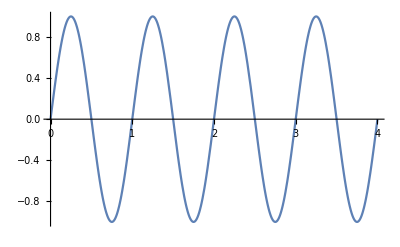

```mathematica
ω=1;Plot[Sin[2π ω x],{x,0,4}]
```

This changes the spatial frequency:

```mathematica
Manipulate[Plot[Sin[2π ω x],{x,0,4},PlotRange->{-1,1}],{{ω,1},0,4}]
```

Here is the frequency shown as a 2D signal, with a spatial frequency along the x-axis, and a constant frequency of zero cycles per meter in the y-direction:

```mathematica
ω=1;spatfreq=Table[Sin[2π ω x],{y,0,4,.01},{x,0,4,.01}];
ArrayPlot[spatfreq]
```

```mathematica
Manipulate[spatfreq=Table[Sin[2π ω x],{y,0,4,.01},{x,0,4,.01}];
ArrayPlot[spatfreq],{{ω,1},0,4}]
```

And here we change the spatial frequencies in the x- and y-direction:

```mathematica
Manipulate[spatfreq=Table[(1+Sin[2π ωx x])(1+Sin[2π ωy y]),{y,0,4,.05},{x,0,4,.05}];
ArrayPlot[spatfreq,PlotRange->All],{{ωx,1},0,4},{{ωy,1},0,4}]
```

```mathematica
Manipulate[spatfreq=Table[(1+Sin[2π ωx x])(1+Sin[2π ωy y]),{y,0,4,.05},{x,0,4,.05}];
ListPlot3D[spatfreq,PlotRange->All],{{ωx,1},0,4},{{ωy,1},0,4}]
```

### The 2D Fourier transform and 2D spectrum

```mathematica
ωx=1;ωy=2;Manipulate[spatfreq=Table[Sin[2π ωx x]Sin[2π ωy y]+μ,{y,0,4,.1},{x,0,4,.1}];
GraphicsGrid[{{,ArrayPlot[spatfreq,PlotRange->{-1,5}],},{ArrayPlot[Re[Fourier[spatfreq]],PlotRange->{0,10}],ArrayPlot[Im[Fourier[spatfreq]],PlotRange->{0,10}],
ArrayPlot[Abs[Fourier[spatfreq]],PlotRange->{0,10}]}}],
{{μ,1},0,2},{{ωx,1},0,4},{{ωy,1},0,4}]
```

The spectrum of white noise is uniform (all frequencies are randomly present in the noise signal):

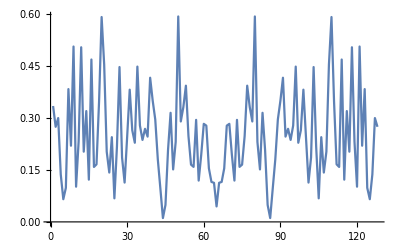

```mathematica
noise=Table[Random[]-.5,{128}];
ListPlot[Abs[Fourier[noise]],Joined->True,PlotRange->All]
```

The Fourier transform of a delta spike is constant, is has a flat spectrum.

```mathematica
FourierTransform[DiracDelta[x],x,ωx]
```

1/(√(2 π))

The spectrum of a point image is completey 'white', all frequencies are present:

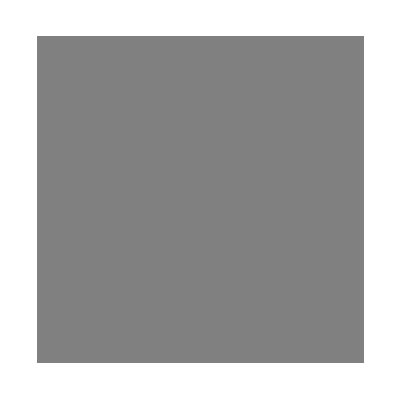

```mathematica
ArrayPlot[s=Abs[Fourier[spike]],PlotRange->{0,0.01}]
```

```mathematica
ListPlot3D[s]
```

-Graphics3D-

## Section. Blurring in the Fourier domain

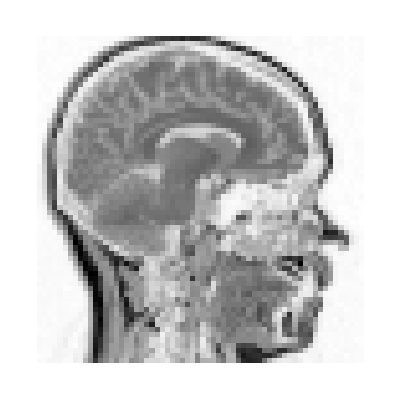

```mathematica
ArrayPlot[mr64=ImageData[Import["http://bmia.bmt.tue.nl/Education/Courses/FEV/book/images/mr64.gif"]]⟦All,All,1⟧]
```

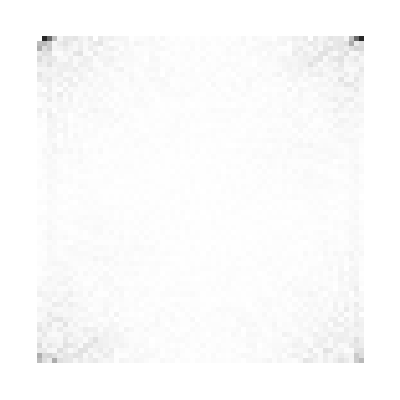

```mathematica
ArrayPlot[Abs[fouriermr64=Fourier[mr64]],PlotRange->{0,5}]
```

```mathematica
σ=1;gaussft=Table[(E^(-1/2 σ^2 (ωx^2+ωy^2)))/(√(2 π)),{ωx,-3.15,3.15,.1},{ωy,-3.15,3.15,.1}];
```

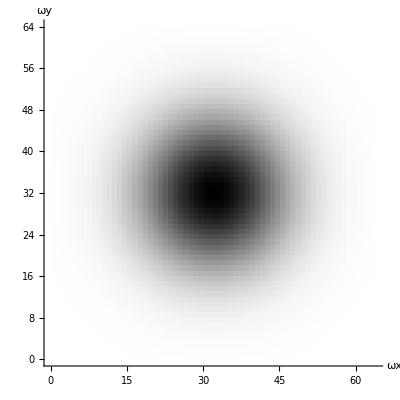

```mathematica
ArrayPlot[gaussft,AxesLabel->{"ωx","ωy"},Axes->True]
```

We shift the Gaussian also to the origin:

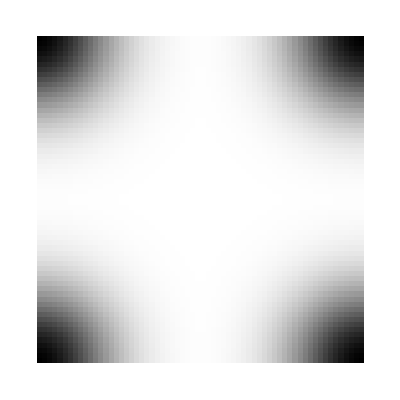

```mathematica
ArrayPlot[shiftedgaussft=RotateLeft[gaussft,Dimensions[gaussft]/2]]
```

Now we are ready to do the filtering in the Fourier domain:

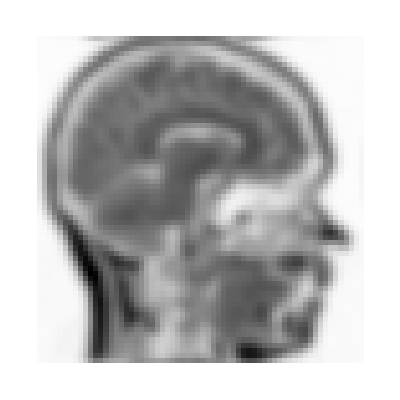

```mathematica
ArrayPlot[Abs[InverseFourier[shiftedgaussft × fouriermr64]],PlotRange->All]
```

```mathematica
Manipulate[gaussft=Table[(E^(-1/2 σ^2 (ωx^2+ωy^2)))/(√(2 π)),{ωx,-3.15,3.15,.1},{ωy,-3.15,3.15,.1}];
shiftedgaussft=RotateLeft[gaussft,Dimensions[gaussft]/2];
GraphicsGrid[{{ArrayPlot[shiftedgaussft],ArrayPlot[Abs[InverseFourier[shiftedgaussft × fouriermr64]],PlotRange->All]}}],{σ,.5,8}]
```